```mathematica
f[c_,Δ_,zir_:10^8]:=(1-2c)/(zir^(1-2c) - 1) 1/(4Δ(Δ-1)) ((zir^(1-2 c)-zir^(-2 Δ))/(1-2 c+2 Δ)+Δ (1/zir^2-zir^(1-2 c))/(3-2 c));
```

```mathematica
f[c,Δ]//StandardForm
```

((1-2 c) (((1/10000000000000000-100000000^(1-2 c)) Δ)/(3-2 c)+(100000000^(1-2 c)-100000000^(-2 Δ))/(1-2 c+2 Δ)))/(4 (-1+100000000^(1-2 c)) (-1+Δ) Δ)

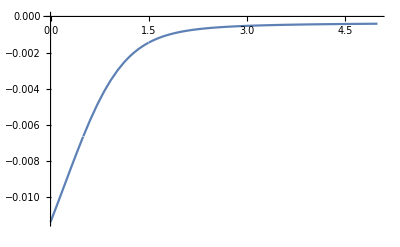

```mathematica
Plot[f[c,9,10],{c,0,5}]
```